```mathematica
a=Import["G:\\calc-online\\gpd\\k-result\\diagram-a-n.wdx"];
f1=Query[1,1]@a;
g1=Query[1,2]@a;
f2=Query[2,1]@a;
g2=Query[2,2]@a;
```

```mathematica
nf1=Simplify[I*f1/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Q^2->1,q3->0.97710345,Λ->1}];
ng1=Simplify[I*g1/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Q^2->1,q3->0.97710345,Λ->1}];
nf2=Simplify[I*f2/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Q^2->1,q3->0.97710345,Λ->1}];
ng2=Simplify[I*g2/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Q^2->1,q3->0.97710345,Λ->1}];
```

```mathematica
ref1[x_]=Simplify[nf1/.{y->x}];
inf1[x_]=Hold[NIntegrate[ref1[x],{k3,0,∞},{θ,0,2π},MaxRecursion->20]];
ref2[x_]=Simplify[nf2/.{y->x}];
inf2[x_]=Hold[NIntegrate[ref2[x],{k3,0,∞},{θ,0,2π},MaxRecursion->20]];
reg1[x_]=Simplify[ng1/.{y->x}];
ing1[x_]=Hold[NIntegrate[reg1[x],{k3,0,∞},{θ,0,2π},MaxRecursion->20]];
reg2[x_]=Simplify[ng2/.{y->x}];
ing2[x_]=Hold[NIntegrate[reg2[x],{k3,0,∞},{θ,0,2π},MaxRecursion->20]];
```

```mathematica
lf1=Table[{x,ReleaseHold[inf1[x]]},{x,-0.094,0.094,0.001}];
lf3=Table[{x,ReleaseHold[inf1[x]]},{x,0.095,0.1,0.00005}];
lf4=Table[{x,ReleaseHold[inf1[x]]},{x,-0.1,-0.095,0.00005}];
lf2=Table[{x,ReleaseHold[inf2[x]]},{x,0.1,1,0.001}];
lg1=Table[{x,ReleaseHold[ing1[x]]},{x,-0.094,0.094,0.001}];lg2=Table[{x,ReleaseHold[ing2[x]]},{x,0.1,1,0.001}];
lg3=Table[{x,ReleaseHold[ing1[x]]},{x,0.095,0.1,0.00005}];
lg4=Table[{x,ReleaseHold[ing1[x]]},{x,-0.1,-0.095,0.00005}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

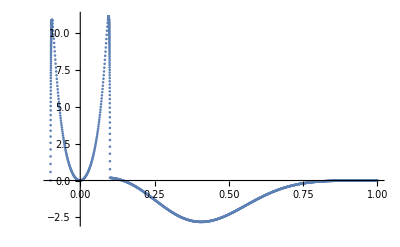

```mathematica
ListPlot[Join[lf4,lf1,lf3,lf2],PlotRange->All]
```

```mathematica
ReleaseHold[inf1[0.1]]
```

0.182827

```mathematica
ReleaseHold[inf2[0.1]]
```

0.182827

```mathematica
ReleaseHold[ing1[0.1]]
ReleaseHold[ing2[0.1]]
```

-1.52692

-1.52692

```mathematica
pf1=Interpolation[Join[lf4,lf1,lf3]];
```

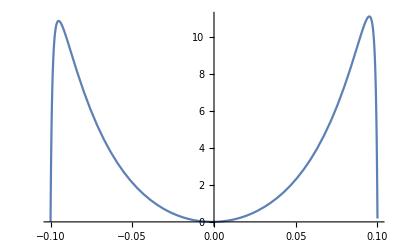

```mathematica
Plot[pf1[x],{x,-0.1,0.1},PlotRange->All]
```

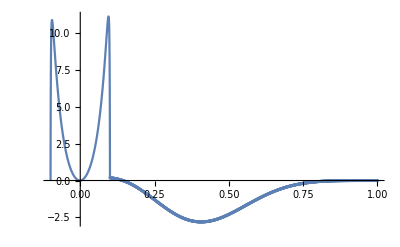

```mathematica
Show[Plot[pf1[x],{x,-0.1,0.1},PlotRange->All],ListPlot[lf2,PlotRange->All]]
```

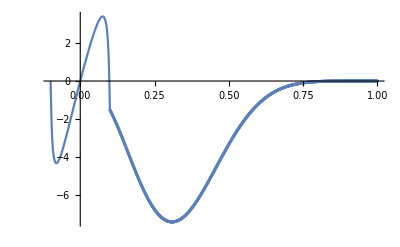

```mathematica
pg1=Interpolation[Join[lg4,lg1,lg3]];
Show[Plot[pg1[x],{x,-0.1,0.1},PlotRange->All],ListPlot[lg2,PlotRange->All]]
```